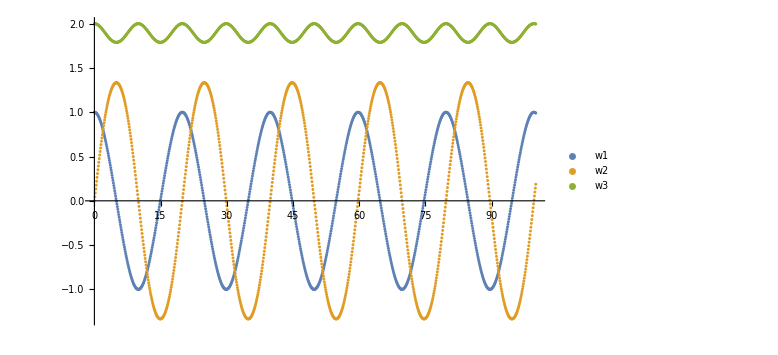

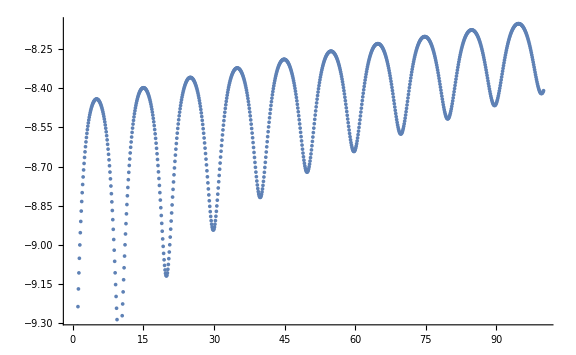

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
Clear["Global`*"]
fw1[i_,w1_,w2_,w3_]:=(I2-I3)/I1*w2*w3
fw2[i_,w1_,w2_,w3_]:=(I3-I1)/I2*w1*w3
fw3[i_,w1_,w2_,w3_]:=(I1-I2)/I3*w1*w2
I1=0.8;
I2=0.9;
I3=1;
imax=1000;
t=Table[i,{i,1,imax+1}];
w1=Table[i,{i,1,imax+1}];
w2=Table[i,{i,1,imax+1}];
w3=Table[i,{i,1,imax+1}];
w1[[1]]=1;
w2[[1]]=0;
w3[[1]]=2;
h=0.1;
t[[1]]=0;
Do[k1w1=fw1[t[[i]],w1[[i]],w2[[i]],w3[[i]]];
k1w2=fw2[t[[i]],w1[[i]],w2[[i]],w3[[i]]];
k1w3=fw3[t[[i]],w1[[i]],w2[[i]],w3[[i]]];
k2w1=fw1[t[[i]]+h/2,w1[[i]]+h/2*k1w1,w2[[i]]+h/2*k1w2,w3[[i]]+h/2*k1w3];
k2w2=fw2[t[[i]]+h/2,w1[[i]]+h/2*k1w1,w2[[i]]+h/2*k1w2,w3[[i]]+h/2*k1w3];
k2w3=fw3[t[[i]]+h/2,w1[[i]]+h/2*k1w1,w2[[i]]+h/2*k1w2,w3[[i]]+h/2*k1w3];
k3w1=fw1[t[[i]]+h/2,w1[[i]]+h/2*k2w1,w2[[i]]+h/2*k2w2,w3[[i]]+h/2*k2w3];
k3w2=fw2[t[[i]]+h/2,w1[[i]]+h/2*k2w1,w2[[i]]+h/2*k2w2,w3[[i]]+h/2*k2w3];
k3w3=fw3[t[[i]]+h/2,w1[[i]]+h/2*k2w1,w2[[i]]+h/2*k2w2,w3[[i]]+h/2*k2w3];
k4w1=fw1[t[[i]]+h,w1[[i]]+h*k3w1,w2[[i]]+h*k3w2,w3[[i]]+h*k3w3];
k4w2=fw2[t[[i]]+h,w1[[i]]+h*k3w1,w2[[i]]+h*k3w2,w3[[i]]+h*k3w3];
k4w3=fw3[t[[i]]+h,w1[[i]]+h*k3w1,w2[[i]]+h*k3w2,w3[[i]]+h*k3w3];
w1[[i+1]]=w1[[i]]+h/6*(k1w1+2*k2w1+2*k3w1+k4w1);
w2[[i+1]]=w2[[i]]+h/6*(k1w2+2*k2w2+2*k3w2+k4w2);
w3[[i+1]]=w3[[i]]+h/6*(k1w3+2*k2w3+2*k3w3+k4w3);
t[[i+1]]=h*i,{i,1,imax}]

w1data=Table[{t[[i]],w1[[i]]},{i,1,imax+1}];
w2data=Table[{t[[i]],w2[[i]]},{i,1,imax+1}];
w3data=Table[{t[[i]],w3[[i]]},{i,1,imax+1}];

Edata=Table[{t[[i]],0.5 (I1*w1[[i]]^2+I2*w2[[i]]^2+I3*w3[[i]]^2)},{i,1,imax+1}];
Energ=0.5*(w1[[1]]^2*I1+w2[[1]]^2*I2+w3[[1]]^2*I3) ;



Energy[w1_,w2_,w3_]:=(I1*w1^2+I2*w2^2+I3*w3^2)/2;
InitEnergy=Energy[w1[[1]],w2[[1]],w3[[1]]];
RltError[w1_,w2_,w3_]:=Log10[Abs[((Energy[w1,w2,w3]-InitEnergy)/InitEnergy)]];
error=Table[{t[[i]],RltError[w1[[i]],w2[[i]],w3[[i]]]},{i,1,imax+1}];

ListPlot[{w1data,w2data,w3data}, PlotLegends->{"w1","w2", "w3"},ImageSize->Large,PerformanceGoal->"Quality"] 
ListPlot[error,ImageSize->Large,PerformanceGoal->"Quality"]
```

```mathematica
(*w1,w2,w3 functions appear to be identical to those provided by the analytical solution.
As we're getting further away from our starting point the error keeps getting higher. That could be happening because the error at nth time step is n times the local truncation error of the Runge-Kutta of 4th order.
It's also worth mentioning that because our functions are periodic, their local maxima and minima occur at the same time. It appears to have an effect on our error as well.
w2 has its critical points (either maxima or minima) happen at the same time with w3 minima. At the same time, the error appears to be the local maximum.
w1 has its critical points (either maxima or minima) happen at the same time with w3 maxima. At the same time, the error appears to be the local minimum.
Finally, this method has a larger error than that of the analytical solution, which is to be expected.
*)
```